```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{14,Directive[FontFamily->"cmr10"]}];
```

# Immirzi 0.1 and i_b=0

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/divergence/cutoff_10.0/frogface_2_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{Indeterminate,5.37891×10^-8,7.94312×10^-8,9.4416×10^-8,9.95934×10^-8,1.02738×10^-7,1.04856×10^-7,1.06373×10^-7,1.07508×10^-7,1.08383×10^-7,1.09075×10^-7,1.09631×10^-7,1.10087×10^-7,1.10464×10^-7,1.1078×10^-7,1.11047×10^-7,1.11275×10^-7,1.11471×10^-7,1.11641×10^-7,1.11788×10^-7,1.11917×10^-7}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,5.37891×10^-8},{1,7.94312×10^-8},{3/2,9.4416×10^-8},{2,9.95934×10^-8},{5/2,1.02738×10^-7},{3,1.04856×10^-7},{7/2,1.06373×10^-7},{4,1.07508×10^-7},{9/2,1.08383×10^-7},{5,1.09075×10^-7},{11/2,1.09631×10^-7},{6,1.10087×10^-7},{13/2,1.10464×10^-7},{7,1.1078×10^-7},{15/2,1.11047×10^-7},{8,1.11275×10^-7},{17/2,1.11471×10^-7},{9,1.11641×10^-7},{19/2,1.11788×10^-7},{10,1.11917×10^-7}}

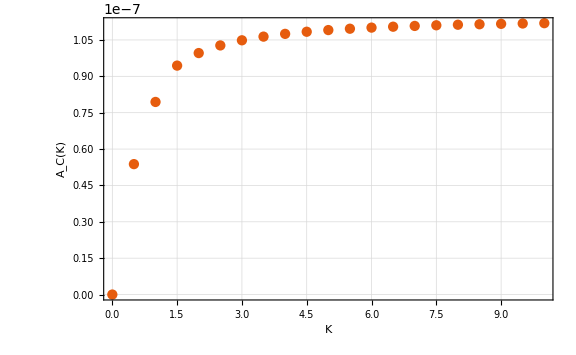

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[1.19808×10^-7+(7.90683×10^-9)/k^2-(4.21162×10^-8)/k-1.63151×10^-9 Log[k]]

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[1.14863×10^-7-(5.01192×10^-9)/k^2-(2.81486×10^-8)/k]

```mathematica
fitExtrap["ParameterConfidenceIntervals"]
```

{{1.14725×10^-7,1.15001×10^-7},{-2.93318×10^-8,-2.69655×10^-8},{-7.09481×10^-9,-2.92904×10^-9}}

```mathematica
fit1 =First/@fitExtrap["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

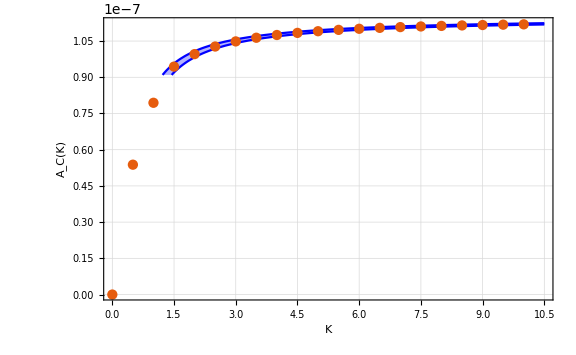

```mathematica
Show[Plot[{fit1,fit2},{k,1,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation,PlotRange->All],PlotRange->All]
```